# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_] := Divide[E^(x+3), 100x + 2]
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x], x]
```

x<-1/50||x>-1/50

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], x -> -1/50, Direction->"FromAbove"]
Limit[f[x], x -> -1/50, Direction->"FromBelow"]
```

∞

-∞

d. Izračunajte odvod funkcije .

```mathematica
df = D[f[x], x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
Solve[df== 0, x]
```

{{x→49/50}}

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
narascanje = Reduce[df > 0, x]
```

x>49/50

```mathematica
padanje =  Reduce[df < 0, x]
```

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

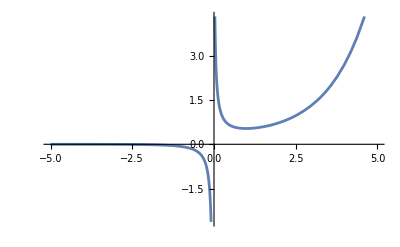

```mathematica
Plot[f[x], {x, -5, 5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x], x, y]
```

y<0||y≥ⅇ^(199/50)/100

i. Izračunajte nedoločeni integral funkcije .

```mathematica
integralf[x_] = Integrate[f[x], x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
V = Pi(integralf[0.5] - integralf[2])^2 // Round[#, 0.001] &
```

2.476

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
Clear[f, df, integralf, x, y]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_] := Divide[1 + x^2.1, 3 + x]
vrednosti = Table[g[x], {x, 1, 101}]
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883,155.621}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
enica[x_] := Mod[IntegerPart[x], 10]
prave = Select[vrednosti, PrimeQ[enica[#]]&]
```

{2.76845,3.79568,7.25393,12.3747,13.7134,15.0702,17.8313,22.0727,23.5093,27.8776,32.3228,33.8198,35.3238,42.9396,47.5778,52.2618,53.8326,55.4079,63.3483,73.005,77.8807,82.7856,87.7183,92.6772,95.9972,97.6613,102.669,107.7,112.754,117.828,122.923,133.171,143.492,145.219,152.146,153.883,155.621}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
prave2 = prave // #^2 + 1 &
```

{8.66433,15.4072,53.6195,154.134,189.057,228.11,318.954,488.203,553.686,778.158,1045.77,1144.78,1248.77,1844.81,2264.65,2732.29,2898.95,3071.03,4014.01,5330.73,6066.4,6854.46,7695.49,8590.07,9216.47,9538.73,10542.,11600.4,12714.4,13884.4,15111.,17735.4,20591.,21089.6,23149.5,23680.9,24218.9}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
prave3 = prave // Floor[#] &
```

{2,3,7,12,13,15,17,22,23,27,32,33,35,42,47,52,53,55,63,73,77,82,87,92,95,97,102,107,112,117,122,133,143,145,152,153,155}

```mathematica
prave4  = Select[prave3, Mod[#, 3] == 0 &] 
Total[prave4]
```

{3,12,15,27,33,42,63,87,102,117,153}

654

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

1+2 x+x^2

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
prep = {x -> y + 1};
 izraz/. prep
```

1+2 (1+y)+(1+y)^2

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
izraz /. x->2
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_] := x^5 - 4x^3 + x^2 + 3x^1 - 2
f2[x_] := f[x] /. {x^n_ ->  2*n * x^(n-1),x-> 2}
f2[x]
```

4+4 x-24 x^2+10 x^4

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x] := x^2025 //. {x^n_ ->  2*n * x^(n-1),x-> 2}
g[x]
```

50398368281427932218648879435231938463740385018981535698812268015338181004233440447381646866294649137295770736080469736945451611684750816765429554471637334740001501598594534331032597748870114113252783072166682814172068709911917364527670863883520516109439601156193945874792418928290668384483145069678513417023938105197860144611773205279706766202805843264139448746199305215127720321701276709845616174477309942850203548438040089622336966153411830490817057562106931531373918440170427190651651291509552173028816653090880390410124613848728073011328868123141697924655871826331444579308611777280419850267069252673270871011426254357267368088452082465883184239579711876955098766888944012424902202472271117002294137662187289730800759111802372042140653613067252559731522689247380713145492578337815032419350558968864802128461806874559617521283051370755651707740483512222942706896220294417736193587422327122493937349053869975080905613341074409856370591228384540547462914934749674719967407166802461771705251988344039091673676298116243611776342480035262913603551206042071315087318298326889285219375078455982381393454535577721929438654313965821718383901579698734794350250889663135600060267632497272846914533248842500900713634107682071942771037059022312127330963916685751533986947045469104263841764085580318979418735565253845707799988662933280173998514215705184510761817648057020681176818220390110689656625808227512142676841258136175561410947541782146102351895347529940329984914134433740808349191681475086917263487402878055232197270993711545771847556111711281997483248420166055210353392934125948685460566822744786039576242387862908516817224599299713349060264891959350554223061569168669110591805940730151727692199083879400823117583782198980698228264952578676889423145009014136180598583831203143150100531144951255305106993279376557370971110685989855895030198617612041846902095867360527064745793077830079135789964591216542266512678813389164497010888450351041236032639088105974609564631099061310599209708371314250526770701710766626107045861787653889003611576409779172464463242707894305376709109642696047509122280055304451115974848420434860156383305962037671954406699655583994795663510601684854237579949676905335113632193064955399389561385744162857819426512767368172765500287185437261645580498135256227942357992233322328859144428344042288725951437817517837464519950437220064136500309507342762578998726422425089837109813055298284976874391723486248221223852607287265397559132595663209783775671975584023422987152768103558329994900247856991510475806100353129547949644060691118916193071914434850692466626683729439853214096339146500243578585257487063051166303039907706415429444803927878750137338266134472773973221472727600949383766106911149634903145266656154915801797612851822101502116797815473067867242247111494164207900579844107703747362187983792806078894693046928886492253793747369477804531754619810737589232942522626385421524638325524024005207820152399363798472344877252389041739723799926442360281798478754277012460923763822491378775442951057966458509377088731192314746431220438947715095621666217601413918543497280977670633747283389886312690158746807940383892702560403217898461005293765397242276719952496820297356405521740190148603296550761503263202284898483307542237932896389095439598745469468063384800981068259953253669057691618851616849675218141468056032841020120124680808128865645517409556038778192444230766517032247554159406211941137968151583011432328046188251111236948498802384774974647508492683293118778961020239136214064956581249828243944208247680407453854634884375433188372353767648773719463340088881082049941589797645059094777824814347927203117365919295367343912642360223907512262369369855838269001900283480240046030415074041883232641405454751307931164835059639251472625956849249357796888050345761694968082204672316345803171760233329560309880471746128202450573837707088603916206020060867328649052538141408261875447873829253175222016646942255218521984469687729585300504283876657214908545122007504505712733546938734232268373353216685193178358011406753089626267197383969407628287524144077822016277383051577009874398005197088665479092679271313594991166607754104348072869807371546305492194633288585969920541760234924234398716156188222734587067016581457508357217265884571170660526794251877640591785974681599769207800403278248496157497691759412755492660679009688014436337345914718972271116999146535015610707610676807866786091272732780062722177003533267392305513905793304800537113795041182031324839883344098203572618875925136662287882826258150143936751296015910445315203133784438388287551424056364616010530628335291868026133228520882011677504896916049976484427353704513206411115070053176842648573953894522165919567029218691394530481648877691448341432146369465338011628835910998889792276758626808532127715478714083278369975889399889416435758457766160915652102935080511752686994145413121791529150371942818032220064420438312771296052695348216049200144764623907049092310297935611369721715215899981986337735370707564487754916502416900076363615082283021894883085394674555526115761223196599572125751561873861912413123623481175538653100059793009154858030691295761299059755675628952479096178480559054665435398504142231434277732945554578761101867219153240449436496974399016155008861275625502155124801551042999516450753098558854479776240953367603643648905146985196295677193844605532089806208809319138340271573956209264727151370742533566263485843394947797489652941301882536037445133724566968842953387012443292641274505072025767819927770557516039669566906323547250244633448367870181579609366206792796631254793079428217242677923356677567603009614313287894711849918301221030984061176855166678119310424558895084058482575915998896906670458144240888397176889456888673162594021398810194225173064220040384348590755559698185143754027548354193622244267987775105811077092684149925836157878779338206740900883049661599937122030108872466708392741885421324072381906671370240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
prep := {{x_, y_} -> {y, x + y}}
fib[num_] := Nest[#/. prep &, {1, 1}, 9 + num][[2]]
fib[1]
```

144